```mathematica
(*Styling of the text*)
st[text_]:=Style[text,Directive[FontSize->15,FontFamily->"Linux Libertine Display"]];
BostonBlue=RGBColor["#00688B"];
```

```mathematica
τ=N [(Sqrt[5]+1)/2];
rot=494;
fib[n_]:=IntegerPart[τ^-1( n+1+rot)]-IntegerPart[τ^-1 (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];
```

```mathematica
(* Hamiltonian in direct space *)
Clear[h];
h[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
(* periodic boundary conditions *)
(*AppendTo[tbl,{1,F2}->jump[F2,tw,ts]];*)
(* potential *)
(*AppendTo[tbl,{40,40}->10.];*)
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* wavefunctions by IDoS *)
n=9+3;
{wf,en}=Block[{val,vec,i=n,ts=1.,tw=0.8,o},
{val,vec}=Eigensystem[h[i,tw,ts]];
(*order wavefunctions by increasing energy*)
o=Ordering[val];
{vec[[o]],val[[o]]}
];
```

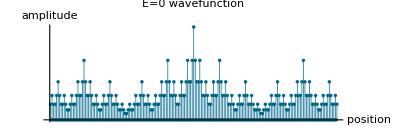

```mathematica
Fibonacci[n+2];
i=189;
ListPlot[Abs[wf[[i]]]^2,PlotRange->All,Filling->Axis,AxesStyle->Directive[Medium,FontFamily->"Linux Libertine Display"],AxesLabel->st/@{"position","amplitude"},PlotLabel->st["E=0 wavefunction"],Ticks->None,AspectRatio->1/3,PlotStyle->{BostonBlue,AbsolutePointSize[2.5]},FillingStyle->AbsoluteThickness[0.5]]
```

```mathematica
Export[NotebookDirectory[]<>"E0_wavefunction.pdf",%]
```

/home/nicolas/git/talks/Aperiodic 2015 Prague/E0_wavefunction.pdf